Data Import

```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210407_sliding_time_windows_and_OR_model"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
datafull=Import["../data/cgl_data_csp_sequences_only.csv",HeaderLines->1];
datafull=Join[Join[datafull[[All,{1,118}]],ConstantArray[{0,0,0,0,0,0},32138],2],datafull[[All,{113,111}]],2];
```

Data with Sliding Time Windows

```mathematica
x1=Round@Ceiling[Length@datafull/10,1];
{a,b,c,d,e,f,g,h,i,j}=Join[Range[x1,Length@datafull,x1],{Length@datafull}];
data1=Join[{Take[datafull,{1,a}]},Flatten[Table[{Take[datafull,{z[[1]]-x1/2,z[[2]]-x1/2}],Take[datafull,{z[[1]],z[[2]]}]},{z,
Partition[{a,b,c,d,e,f,g,h,i,j},2,1]}],1]];
win1=Length@data1;
```

```mathematica
x2=Round@Ceiling[Length@datafull/19,1];
{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,r,s,t}=Join[Range[x2,Length@datafull,x2],{Length@datafull}];
data2=Join[{Take[datafull,{1,a}]},Flatten[Table[{Take[datafull,{z[[1]]-x2/2,z[[2]]-x2/2}],Take[datafull,{z[[1]],z[[2]]}]},{z,
Partition[{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,r,s,t},2,1]}],1]];
win2=Length@data2;
```

Investigation of Constraints Impact in Time Windows

Fixed Step Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep1=snetworkdatabinnedintimewindows[data1,9,11,win1];]
```

{6.91148,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedstep1[[1]][[i]],widthdataintimewindowsFixedstep1[[2]][[i]],2,7,400,Green],{i,Range@win1}];
modularityvalues1=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues1=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity1=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{273.142,Null}

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep2=snetworkdatabinnedintimewindows[data2,9,11,win2];]
```

{6.92609,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedstep2[[1]][[i]],widthdataintimewindowsFixedstep2[[2]][[i]],2,7,400,Green],{i,Range@win2}];
modularityvalues2=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues2=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity2=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{512.468,Null}

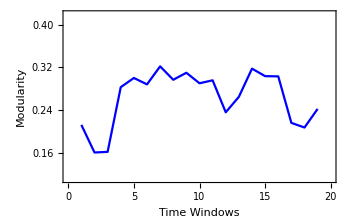
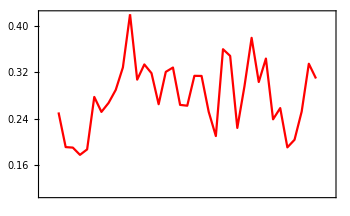
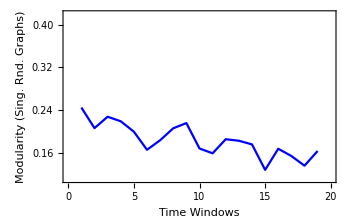
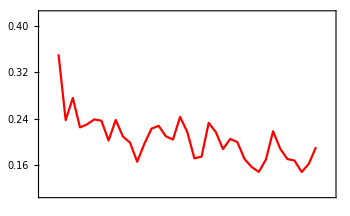
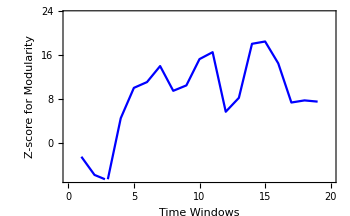
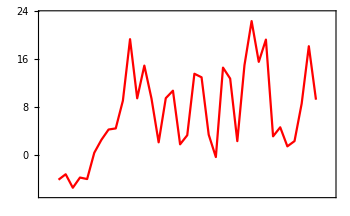

```mathematica
{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{0.11,0.42}}],ListLinePlot[Thread[{Range@win2,modularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{0.11,0.42}}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,singlerandomcommmodularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{0.11,0.42}}],ListLinePlot[Thread[{Range@win2,singlerandomcommmodularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{0.11,0.42}}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,Zscoresmodularity1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-score for Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{-6.5,23.5}}],ListLinePlot[Thread[{Range@win2,Zscoresmodularity2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{-6.5,23.5}}]}]}
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedstep1=snetworkdatabinnedintimewindows[data1,10,0.05,win1];]
```

{3.79998,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedstep1[[1]][[i]],thicknessdataintimewindowsFixedstep1[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win1}];
modularityvalues1=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues1=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity1=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{189.199,Null}

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedstep2=snetworkdatabinnedintimewindows[data2,10,0.05,win2];]
```

{3.7245,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedstep2[[1]][[i]],thicknessdataintimewindowsFixedstep2[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win2}];
modularityvalues2=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues2=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity2=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{283.407,Null}

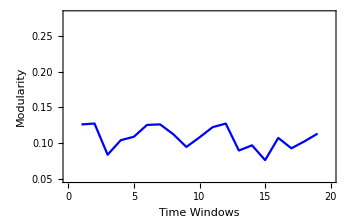
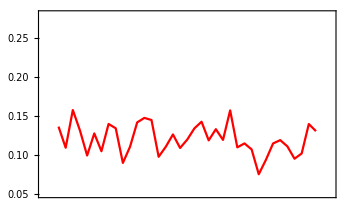
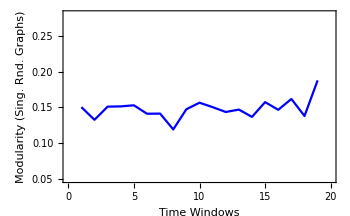
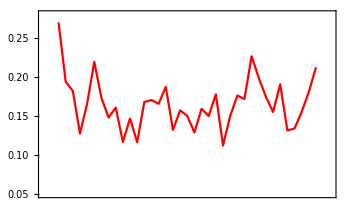
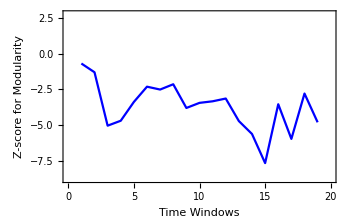
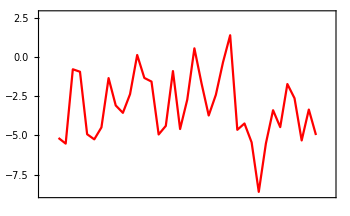

```mathematica
{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{0.05,0.28}}],ListLinePlot[Thread[{Range@win2,modularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{0.05,0.28}}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,singlerandomcommmodularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{0.05,0.28}}],ListLinePlot[Thread[{Range@win2,singlerandomcommmodularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{0.05,0.28}}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,Zscoresmodularity1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-score for Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{-8.75,2.75}}],ListLinePlot[Thread[{Range@win2,Zscoresmodularity2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{-8.75,2.75}}]}]}
```

Fixed Bucket Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket1=snetworkdatafxdbucketintimewindows[data1,9,65,win1];]
```

{1.00392,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedbucket1[[1]][[i]],widthdataintimewindowsFixedbucket1[[2]][[i]],1.5,7,400,Green],{i,Range@win1}];
modularityvalues1=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues1=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity1=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{211.637,Null}

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket2=snetworkdatafxdbucketintimewindows[data2,9,65,win2];]
```

{1.01932,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedbucket2[[1]][[i]],widthdataintimewindowsFixedbucket2[[2]][[i]],1.5,7,400,Green],{i,Range@win2}];
modularityvalues2=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues2=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity2=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{602.312,Null}

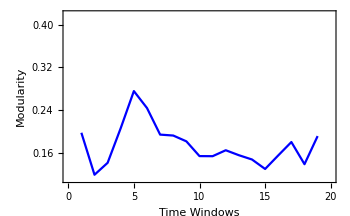
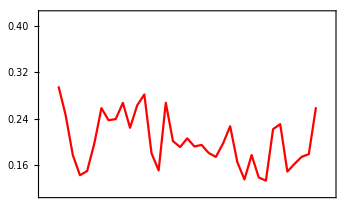
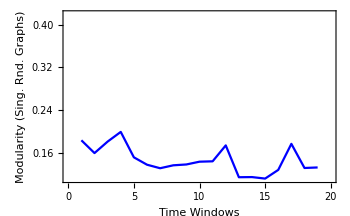
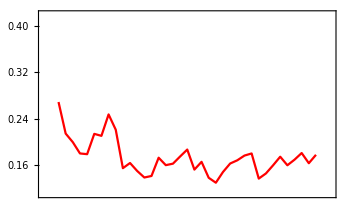
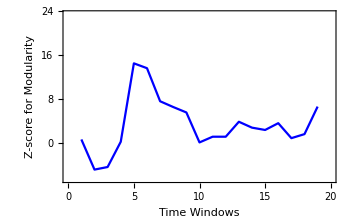
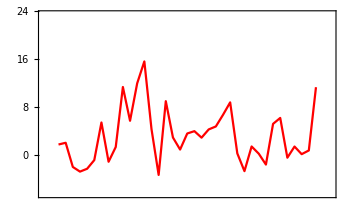

```mathematica
{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{0.11,0.42}}],ListLinePlot[Thread[{Range@win2,modularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{0.11,0.42}}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,singlerandomcommmodularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{0.11,0.42}}],ListLinePlot[Thread[{Range@win2,singlerandomcommmodularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{0.11,0.42}}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,Zscoresmodularity1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-score for Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{-6.5,23.5}}],ListLinePlot[Thread[{Range@win2,Zscoresmodularity2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{-6.5,23.5}}]}]}
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedbucket1=snetworkdatafxdbucketintimewindows[data1,10,47,win1];]
```

{1.02598,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedbucket1[[1]][[i]],thicknessdataintimewindowsFixedbucket1[[2]][[i]],1.5,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win1}];
modularityvalues1=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues1=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity1=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{174.44,Null}

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedbucket2=snetworkdatafxdbucketintimewindows[data2,10,47,win2];]
```

{0.992038,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedbucket2[[1]][[i]],thicknessdataintimewindowsFixedbucket2[[2]][[i]],1.5,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win2}];
modularityvalues2=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues2=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity2=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{396.265,Null}

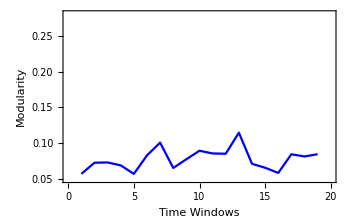
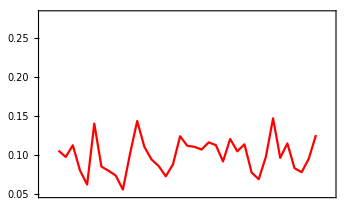
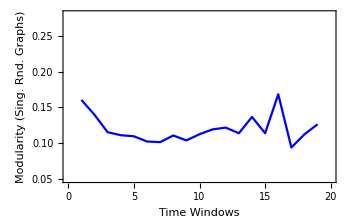
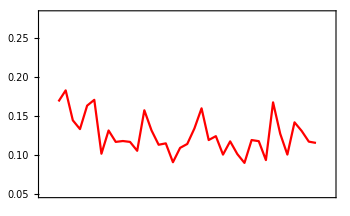
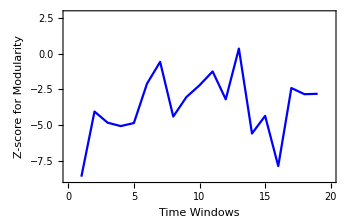
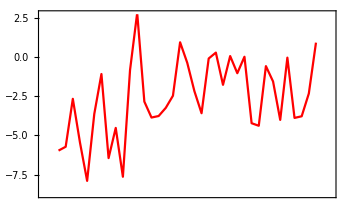

```mathematica
{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{0.05,0.28}}],ListLinePlot[Thread[{Range@win2,modularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{0.05,0.28}}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,singlerandomcommmodularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{0.05,0.28}}],ListLinePlot[Thread[{Range@win2,singlerandomcommmodularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{0.05,0.28}}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,Zscoresmodularity1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-score for Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{-8.75,2.75}}],ListLinePlot[Thread[{Range@win2,Zscoresmodularity2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{-8.75,2.75}}]}]}
```

Plots for Network Metrics and Z-scores